These ranges are the ones I computed when fitting the model for three different regions (Mala Mala, Kruger, Serengeti). The values we had for the Serengeti are the values we put in the Egypt paper:

b0 = 1.41, b1 = 3.73, and b2 = −1.87 using the log of the body mass

b0 = 2.51, b1 = 0.79, and b2 = −0.37 using the raw values (which makes more sense)

In the PRSB paper I sampled values from the ranges of MLEs computed for the three regions (with no log transformation):

b0=1.6332+(3.4895-1.6332)*rand(1);
b1=0.2109+(0.7912-0.2109)*rand(1);
b2=-0.3731+(-0.3045-(-0.3731))*rand(1);

```mathematica
α = 1.6332
β =0.2109
γ = -0.3731
```

1.6332

0.2109

-0.3731

(ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))/(1+ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))

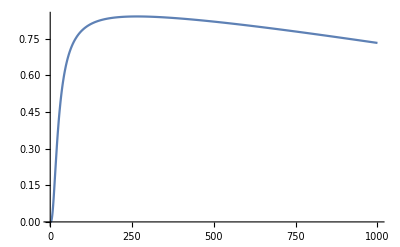

```mathematica
pMathias = Exp[alpha + beta*Log[PredMass/PreyMass] + gamma*Log[PredMass/PreyMass]^2];
probMathias = p/(1+p)
Plot[probMathias/.{alpha->1.6332,beta->0.2109,gamma->-0.3731,PredMass->200},{PreyMass,1,10^3},PlotRange->All]
```

```mathematica
p = Exp[alpha + beta*Log[PreyMass/PredMass] + gamma*Log[PreyMass/PredMass]^2];
prob = p/(1+p)
```

(ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))/(1+ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))

```mathematica
D[prob,PreyMass]
```

-(ⅇ^(2 alpha+2 beta Log[PreyMass/PredMass]+2 gamma Log[PreyMass/PredMass]^2) (beta/PreyMass+(2 gamma Log[PreyMass/PredMass])/PreyMass))/((1+ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))^2)+(ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2) (beta/PreyMass+(2 gamma Log[PreyMass/PredMass])/PreyMass))/(1+ⅇ^(alpha+beta Log[PreyMass/PredMass]+gamma Log[PreyMass/PredMass]^2))

```mathematica
OptMass =Solve[ D[prob,PreyMass]==0,PredMass]
```

{{PredMass→ⅇ^(beta/(2 gamma)) PreyMass}}

From my own fitting of the Baskerville data and with mi/mj = preymass/predmass
 2.0558989052412504
 -1.918476481051926
  0.047825684997587214

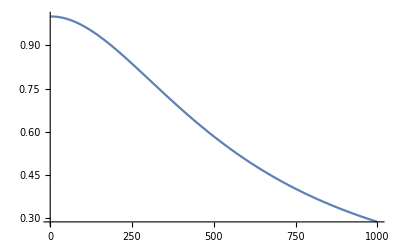

```mathematica
Plot[prob/.{alpha->2.0558989052412504,beta->-1.918476481051926,gamma->0.047825684997587214,PredMass->200},{PreyMass,1,10^3}]
```

```mathematica
Solve[Mc==1.4*Mp^0.9,Mp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Mp→0.688075 Mc^1.11111111111111}}

```mathematica
Solve[Mc==Exp[0.2]*Mp^1.16,Mp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Mp→0.841631 Mc^0.862068965517241}}

```mathematica
Solve[Mc==Exp[0.904]*Mp^0.711,Mp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Mp→0.280425 Mc^1.40646976090014}}

```mathematica
Solve[Mc==Exp[1.43]*Mp^0.83,Mp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Mp→0.178549 Mc^1.20481927710843}}

```mathematica
Solve[Mc==Exp[1.60]*Mp^0.87,Mp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Mp→0.158964 Mc^1.14942528735632}}